```mathematica
Homework 5
```

```mathematica
John Knowles
```

```mathematica
{{Rule (->), ReplaceAll (/.), ReplaceRepeated (//.), MaxIterations, Quiet, MatchQ}, {Cases, ReplaceList, Permutations, IntegerExponent, Module, Short}}
```

```mathematica
Clear["Global`*"]
```

## 1. Problem 8.1

```mathematica
Permutations[{x,y,z}]
Permutations[{x,y,z}]/.{a_,b_,c_}->a^b^c
```

{{x,y,z},{x,z,y},{y,x,z},{y,z,x},{z,x,y},{z,y,x}}

{x^(y^z),x^(z^y),y^(x^z),y^(z^x),z^(x^y),z^(y^x)}

## 2. Exercise 8.1

```mathematica
(a+b)^n/.(x_+y_)^z_->(x^z+y^z)
```

a^n+b^n

```mathematica
(* This function is replaced with an expression where the exponent is directly applied to the variables. The two expressions are not equivalent. *)
```

## 3. Exercise 8.2

```mathematica
??Manipulate
```

RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a version of StyleBox["expr", "TI"] with controls added to allow interactive manipulation of the value of StyleBox["u", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["du", "TI"]}], "}"}]}], "]"}] allows the value of StyleBox["u", "TI"] to vary between SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]] in steps StyleBox["du", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]}], "}"}], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] takes the initial value of StyleBox["u", "TI"] to be SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] labels the controls for StyleBox["u", "TI"] with SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] allows StyleBox["u", "TI"] to take on discrete values RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] provides controls to manipulate each of the RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["u", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["v", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["…", "TR"]}], "]"}] links the controls to the specified controllers on an external device.

Attributes[Manipulate]={HoldAll,Protected,ReadProtected}
 
Options[Manipulate]={Alignment→Automatic,AppearanceElements→Automatic,AutoAction→False,AutorunSequencing→Automatic,BaselinePosition→Automatic,BaseStyle→{},Bookmarks→{},ContentSize→Automatic,ContinuousAction→Automatic,ControlAlignment→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,ControlPlacement→Automatic,ControlType→Automatic,DefaultBaseStyle→Manipulate,DefaultLabelStyle→ManipulateLabel,Deinitialization:>None,Deployed→False,Evaluator→Automatic,Frame→False,FrameLabel→None,FrameMargins→Automatic,ImageMargins→0,Initialization:>None,InterpolationOrder→Automatic,LabelStyle→{},LocalizeVariables→True,Method→{},Paneled→True,PreserveImageOptions→True,RotateLabel→False,SaveDefinitions→False,ShrinkingDelay→0,SynchronousInitialization→True,SynchronousUpdating→Automatic,TouchscreenAutoZoom→False,TouchscreenControlPlacement→Automatic,TrackedSymbols→Full,UndoTrackedVariables:>None,UnsavedVariables:>None,UntrackedVariables:>None}

```mathematica
{0}/.{0->{0,1},1->{1,0}};
{{0,1}}/.{0->{0,1},1->{1,0}};
{{{0,1},{1,0}}}/.{0->{0,1},1->{1,0}}//Flatten//FromDigits;
morse[n_]:=Quiet[FromDigits[Flatten[ReplaceRepeated[{0},{0->{0,1},1->{1,0}},MaxIterations->n]]]]
morse[5]
Manipulate[Quiet[Flatten[ReplaceRepeated[{x},{x->{x,y},y->{y,x}},MaxIterations->i]]],{i,1,20,1}]
```

1101001100101101001011001101001

## 4. Problem 9.1 ****

```mathematica
squareFreeQ[n_?IntegerQ]:=Cases[FactorInteger[n],{_,_(#>1&)}]=={}
FactorInteger[23423]
squareFreeQ[23423]
```

{{59,1},{397,1}}

True

## 5. Exercise 9.1

```mathematica
dataSample=Table[Random[Integer,{1,10}],{1000}];
Apply[Plus, dataSample/. 1->"a"/.x_Integer->0/."a"->1];
frequence[data_List,n_]:=Apply[Plus,data/.n->"a"/.x_Integer->0/."a"->1]
Table[frequence[dataSample,n],{n,1,10}]
```

{97,95,106,97,104,122,96,117,84,82}

```mathematica
(* A set of 1000 random integers 1-10 are fed into a filtering function which operates by changing the value in the dataSample to "a" after matching to n. Once it is no longer an integer, all other elements in that iteration are changed to 0. The elements in dataSample are summed up, therefore giving the frequency of which n shows up in a random data sample.*)
```

## 6. Problem 9.2

```mathematica
FromDigits/@Select[IntegerDigits/@Prime/@Range[1,50000], MatchQ[#,{m___,2,0,0,9,n___}]&]
```

{32009,52009,82009,92009,120091,120097,172009,182009,200903,200909,200927,200929,200971,200983,200987,200989,242009,272009,302009,322009,332009,420097,442009,452009,512009,532009}

## 7. Exercise 9.2

```mathematica
Range[10]/.{x_,y__}->y/x==10!
```

True

## 8. Problem 9.3

```mathematica
s=Table[RandomInteger[{1,9}],{7}]
s2=s/.{m___,x_?(3<#<10&),y___,x_,n___}->{m,y,n}
Plus@@ s2
```

{6,5,7,7,6,7,3}

{5,7,7,7,3}

29

## 9. Problem 9.4 ****

```mathematica
?ReplaceList
```

RowBox[{"ReplaceList", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["rules", "TI"]}], "]"}] attempts to transform the entire expression StyleBox["expr", "TI"] by applying a rule or list of rules in all possible ways, and returns a list of the results obtained. 
RowBox[{"ReplaceList", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["rules", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives a list of at most StyleBox["n", "TI"] results.

```mathematica
(* /. cannot be used inside ReplaceList & ReplaceList ≠ Replace*)
Select[Range[10000,99999],MemberQ[Plus @@@ Map[FromDigits,ReplaceList[IntegerDigits[#^2],{x__,y__}->{{x},{y}}]/.{m_,__?PossibleZeroQ}->Sequence[],{2}],#]&]
```

{17344,22222,38962,77778,82656,95121,99999}

## 10. Exercise 9.3

```mathematica
Select[DictionaryLookup[],MatchQ[Characters[#],{___,"r","a","t"}]&]
```

{Ararat,aristocrat,autocrat,baccarat,brat,bureaucrat,carat,democrat,Democrat,Dixiecrat,drat,frat,Gujarat,karat,Marat,Montserrat,Murat,muskrat,plutocrat,prat,rat,Seurat,sprat,Surat,technocrat}

## 11. Problem 9.5

```mathematica
Short[Select[DictionaryLookup[],MatchQ[Characters[#],{___,"c",___,"u",___,"t",___,"e",___}]&]]
%//Length
```

{accentuate,accentuated,accentuates,«699»,viticulture,woodcutter,woodcutters}

705

## 12. Problem 9.6

```mathematica
syracuseOld[n_?OddQ]:=Times@@(Rest[FactorInteger[3n+1]]/.{x_Integer,y_}->x^y)
syracuseNew[n_]:=Quotient[3n+1,2^IntegerExponent[3n+1,2]]
FixedPointList[syracuseOld,123]
FixedPointList[syracuseNew,123]
```

{123,185,139,209,157,59,89,67,101,19,29,11,17,13,5,1,1}

{123,185,139,209,157,59,89,67,101,19,29,11,17,13,5,1,1}

## 13. Problem 10.1

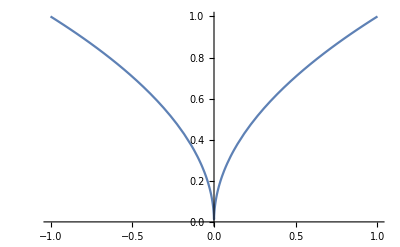

```mathematica
Clear[f]
f[x_?Positive]:=Sqrt[x]
f[x_?Negative]:=Sqrt[-x]
Plot[f[x],{x,-1,1}]
```

## 14. Problem 10.2

{1,2,8,3,6,9,17,4,20,7,15,10,10,18,18,5,13,21,21,8,8,16,16,11,24,11,112,19,19,19,107,6,27,14,14,22,22,22,35,9,110,9,30,17,17,17,105,12,25,25,25,12,12,113,113,20,33,20,33,20,20,108,108,7,28,28,28,15,15,15,103,23,116,23,15,23,23,36,36,10,23,111,111,10,10,31,31,18,31,18,93,18,18,106,106,13,119,26,26,26,26,26,88,13,39,13,101,114,114,114,70,21,13,34,34,21,21,34,34,21,96,21,47,109,109,109,47,8,122,29,29,29,29,29,42,16,91,16,42,16,16,104,104,24,117,117,117,24,24,16,16,24,37,24,86,37,37,37,55,11,99,24,24,112,112,112,68,11,50,11,125,32,32,32,81,19,32,32,32,19,19,94,94,19,45,19,45,107,107,107,45,14,120,120,120,27,27,27,120,27}

125

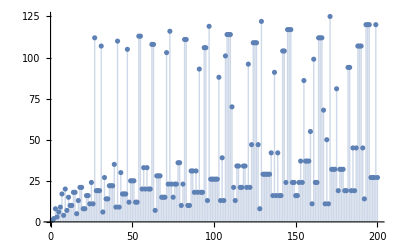

```mathematica
Clear[f]
f[x_Integer?EvenQ]:=x/2
f[x_Integer]:=3 x+1
l=Length/@(NestWhileList[f,#,!#==1&]&/@Range[200])
Max[l]
ListPlot[l,Filling->Axis]
```

## 15. Problem 10.3

```mathematica
Clear[f]
f[x_ y_]:=f[x]+f[y]
f[x_^n_Integer]:=n f[x]
f[n_Integer]=0;
f[Product[i Subscript[x,i]^i,{i,1,20}]]
%==Sum[i f[Subscript[x,i]],{i,1,20}]
```

f[x_1]+2 f[x_2]+3 f[x_3]+4 f[x_4]+5 f[x_5]+6 f[x_6]+7 f[x_7]+8 f[x_8]+9 f[x_9]+10 f[x_10]+11 f[x_11]+12 f[x_12]+13 f[x_13]+14 f[x_14]+15 f[x_15]+16 f[x_16]+17 f[x_17]+18 f[x_18]+19 f[x_19]+20 f[x_20]

True

## 16. Problem 10.4

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

```mathematica
o[n___,y_,t___,z_,m___]:=o[n,t,m]/;y+z==5
hand=Module[{},o[Apply[Sequence,Table[RandomInteger[{1,9}],{7}]]]]
Print[Plus@@%]
```

o[8,1,1,1,9]

20

## 17. ****

```mathematica
a=CharacterRange["2","9"];
originalDeck=Flatten[Outer[StringJoin,Join[{"A"},AppendTo[a,"10"],{"J","Q","K"}],{"♣","♡","♢","♠"}]];
f[x__]:=Riffle@@Partition[x,26];
NestWhileList[f[#]&,#,UnsameQ,All]&[originalDeck]
Print["An Out Faro shuffle returns to the original deck position after ",(%//Length)-1, " shuffles."]
```

{{A♣,A♡,A♢,A♠,2♣,2♡,2♢,2♠,3♣,3♡,3♢,3♠,4♣,4♡,4♢,4♠,5♣,5♡,5♢,5♠,6♣,6♡,6♢,6♠,7♣,7♡,7♢,7♠,8♣,8♡,8♢,8♠,9♣,9♡,9♢,9♠,10♣,10♡,10♢,10♠,J♣,J♡,J♢,J♠,Q♣,Q♡,Q♢,Q♠,K♣,K♡,K♢,K♠},{A♣,7♢,A♡,7♠,A♢,8♣,A♠,8♡,2♣,8♢,2♡,8♠,2♢,9♣,2♠,9♡,3♣,9♢,3♡,9♠,3♢,10♣,3♠,10♡,4♣,10♢,4♡,10♠,4♢,J♣,4♠,J♡,5♣,J♢,5♡,J♠,5♢,Q♣,5♠,Q♡,6♣,Q♢,6♡,Q♠,6♢,K♣,6♠,K♡,7♣,K♢,7♡,K♠},{A♣,4♡,7♢,10♠,A♡,4♢,7♠,J♣,A♢,4♠,8♣,J♡,A♠,5♣,8♡,J♢,2♣,5♡,8♢,J♠,2♡,5♢,8♠,Q♣,2♢,5♠,9♣,Q♡,2♠,6♣,9♡,Q♢,3♣,6♡,9♢,Q♠,3♡,6♢,9♠,K♣,3♢,6♠,10♣,K♡,3♠,7♣,10♡,K♢,4♣,7♡,10♢,K♠},{A♣,9♣,4♡,Q♡,7♢,2♠,10♠,6♣,A♡,9♡,4♢,Q♢,7♠,3♣,J♣,6♡,A♢,9♢,4♠,Q♠,8♣,3♡,J♡,6♢,A♠,9♠,5♣,K♣,8♡,3♢,J♢,6♠,2♣,10♣,5♡,K♡,8♢,3♠,J♠,7♣,2♡,10♡,5♢,K♢,8♠,4♣,Q♣,7♡,2♢,10♢,5♠,K♠},{A♣,5♣,9♣,K♣,4♡,8♡,Q♡,3♢,7♢,J♢,2♠,6♠,10♠,2♣,6♣,10♣,A♡,5♡,9♡,K♡,4♢,8♢,Q♢,3♠,7♠,J♠,3♣,7♣,J♣,2♡,6♡,10♡,A♢,5♢,9♢,K♢,4♠,8♠,Q♠,4♣,8♣,Q♣,3♡,7♡,J♡,2♢,6♢,10♢,A♠,5♠,9♠,K♠},{A♣,3♣,5♣,7♣,9♣,J♣,K♣,2♡,4♡,6♡,8♡,10♡,Q♡,A♢,3♢,5♢,7♢,9♢,J♢,K♢,2♠,4♠,6♠,8♠,10♠,Q♠,2♣,4♣,6♣,8♣,10♣,Q♣,A♡,3♡,5♡,7♡,9♡,J♡,K♡,2♢,4♢,6♢,8♢,10♢,Q♢,A♠,3♠,5♠,7♠,9♠,J♠,K♠},{A♣,2♣,3♣,4♣,5♣,6♣,7♣,8♣,9♣,10♣,J♣,Q♣,K♣,A♡,2♡,3♡,4♡,5♡,6♡,7♡,8♡,9♡,10♡,J♡,Q♡,K♡,A♢,2♢,3♢,4♢,5♢,6♢,7♢,8♢,9♢,10♢,J♢,Q♢,K♢,A♠,2♠,3♠,4♠,5♠,6♠,7♠,8♠,9♠,10♠,J♠,Q♠,K♠},{A♣,A♢,2♣,2♢,3♣,3♢,4♣,4♢,5♣,5♢,6♣,6♢,7♣,7♢,8♣,8♢,9♣,9♢,10♣,10♢,J♣,J♢,Q♣,Q♢,K♣,K♢,A♡,A♠,2♡,2♠,3♡,3♠,4♡,4♠,5♡,5♠,6♡,6♠,7♡,7♠,8♡,8♠,9♡,9♠,10♡,10♠,J♡,J♠,Q♡,Q♠,K♡,K♠},{A♣,A♡,A♢,A♠,2♣,2♡,2♢,2♠,3♣,3♡,3♢,3♠,4♣,4♡,4♢,4♠,5♣,5♡,5♢,5♠,6♣,6♡,6♢,6♠,7♣,7♡,7♢,7♠,8♣,8♡,8♢,8♠,9♣,9♡,9♢,9♠,10♣,10♡,10♢,10♠,J♣,J♡,J♢,J♠,Q♣,Q♡,Q♢,Q♠,K♣,K♡,K♢,K♠}}

An Out Faro shuffle returns to the original deck position after 8 shuffles.

## 18.

```mathematica
permN[n_Integer?Positive]:=Count[MatchQ[{___,a_,b_,c_,___}/;(a<b<c)]/@Permutations[Range[n]],False]
permN[8]
SequenceCases[RandomChoice[Permutations[Range[8]]],{___,a_,b_,c_,___}/;!(a<b<c)]
Count[Select[{___,a_,b_,c_,___}/;(a<b<c)]/@Permutations[Range[9]],False]
permN[8]
```

13358

{{3,5,6,7,4,1,8,2}}

0

13358

## 19.

```mathematica
AntiDerivative[n_Integer]:=n x+C
AntiDerivative[Power[x_Symbol,n_Integer]]:=(1/(n+1))Power[x,n+1]+C
AntiDerivative[Power[n_Integer?Positive,x_Symbol]]:=Power[n,x]/Log[n]+C
AntiDerivative[Plus[Power[x_Symbol,n_Integer],Power[m_Integer,y_Symbol]]]:=Plus[AntiDerivative[x^n],AntiDerivative[m^y]]

AntiDerivative[a_Integer,
Times[b_Integer,x_Symbol],
Times[c_Integer,Power[x_Symbol,d_Integer]],
Power[e_Integer,x_Symbol],
Times[f_Integer,Power[g_Integer,x_Symbol]]]:=AntiDerivative[a]+AntiDerivative[b x]+AntiDerivative[Times[c,d^y]]+Plus[AntiDerivative[e^z],Times[f,Power[g,xx]]]
```

```mathematica
AntiDerivative[3]
AntiDerivative[x^2]
AntiDerivative[3^x]
AntiDerivative[x^2+3^x]
AntiDerivative[112+4*x+12*x^5+7^x+3*5^x]
AntiDerivative[x^x]
AntiDerivative[x^t]
AntiDerivative[(-5)^x]
AntiDerivative[x,2]
```

C+3 x

C+x^3/3

C+3^x/Log[3]

2 C+x^3/3+3^x/Log[3]

AntiDerivative[112+3 5^x+7^x+4 x+12 x^5]

AntiDerivative[x^x]

AntiDerivative[x^t]

C+(-5)^x/(ⅈ π+Log[5])

AntiDerivative[x,2]